```mathematica
$Path=Append[$Path,"C:\\Users\\telea\\OneDrive\\Documents\\MATLAB\\SDv3.5.0\\SDv3.5.0\\SpinDynamica"];
Needs["SpinDynamica`"];
```

SpinDynamica version 3.5.0b1m loaded

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Dot,Duration,Exp,Expand,Plus,Power,Simplify,Times,WignerD}

# Set spin system

```mathematica
SetSpinSystem[2]
SetBasis[ZeemanBasis[]]
SetOperatorBasis[CartesianProductOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

SetBasis::alreadyset: The basis is already set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic]. No action has been taken.

SetOperatorBasis::set: the operator basis has been set to CartesianProductOperatorBasis[{{1,1/2},{2,1/2}},Sorted→SpinProductRank].

# Define pulse sequence

```mathematica
ωnuthard=2π*50*10^3;τ360=(2π)/ωnuthard; τ180=τ360/2;τ90= τ360/4; τ45=τ90/2;
H[Ω1_,Ω2_,J_]:=Ω1*opI[1,"z"]+Ω2*opI[2,"z"]+2π*J*opI[1].opI[2];
Hx[Ω1_,Ω2_,J_]:=H[Ω1,Ω2,J]+ωnuthard*opI["x"];
Hy[Ω1_,Ω2_,J_]:=H[Ω1,Ω2,J]+ωnuthard*opI["y"];
HSLIC[Ω1_,Ω2_,J_]:=H[Ω1,Ω2,J]+2π*J*opI["x"];
```

```mathematica
M2SevS2M[Ω1_,Ω2_,J_,τ_,n1_,n2_]:={{Hy[Ω1,Ω2,J],τ90},Repeat[{{H[Ω1,Ω2,J],τ},{Hx[Ω1,Ω2,J],τ90},{Hy[Ω1,Ω2,J],τ180},{Hx[Ω1,Ω2,J],τ90},{H[Ω1,Ω2,J],τ}},n1],{Hx[Ω1,Ω2,J],τ90},{H[Ω1,Ω2,J],τ},Repeat[{{H[Ω1,Ω2,J],τ},{Hx[Ω1,Ω2,J],τ90},{Hy[Ω1,Ω2,J],τ180},{Hx[Ω1,Ω2,J],τ90},{H[Ω1,Ω2,J],τ}},n2],{H[Ω1,Ω2,J],0.5}};
SLIC[Ω1_,Ω2_,J_,τev_]:={{Hy[Ω1,Ω2,J],τ90},{HSLIC[Ω1,Ω2,J],(2π)/((Ω2-Ω1)*√2)},{H[Ω1,Ω2,J],τev}};
SarkarSeqII[Ω1_,Ω2_,J_,τev_]:={{Hx[Ω1,Ω2,J],τ90},{H[Ω1,Ω2,J],1/(4*J)},{Hx[Ω1,Ω2,J],τ180},{H[Ω1,Ω2,J],1/(4J)},{Hy[Ω1,Ω2,J],τ90/2},CoherenceOrderFiltrationSuperoperator[{1,2},{0}],{H[Ω1,Ω2,J],(2π)/(2Abs[Ω2-Ω1])},{H[Ω1,Ω2,J],τev}}
```

# Compare weak and strong coupled regime

```mathematica
BasisOperators[SingletTripletOperatorBasis[]];
SS=BasisOperators[SingletTripletOperatorBasis[]][[11]];
T0=BasisOperators[SingletTripletOperatorBasis[]][[9]];
```

## M2S comparison

```mathematica
n1[Ω1_,Ω2_,J_]:=Round[π/(2*ArcTan[Abs[(Ω1-Ω2)/(2π*J)]])]
```

```mathematica
Ω1=-2π*1.4;Ω2=2π*1.4;J=17.4;
```

```mathematica
trajSS1strong=Trajectory[opI["z"]->{-SS},M2SevS2M[Ω1,Ω2,J,1/(4J),n1[Ω1,Ω2,J],n1[Ω1,Ω2,J]/2]];
```

```mathematica
Ω1=-2π*25;Ω2=2π*25;J=17.4;
```

```mathematica
trajSS1weak=Trajectory[opI["z"]->{-SS},M2SevS2M[Ω1,Ω2,J,1/(4J),10,5]];
```

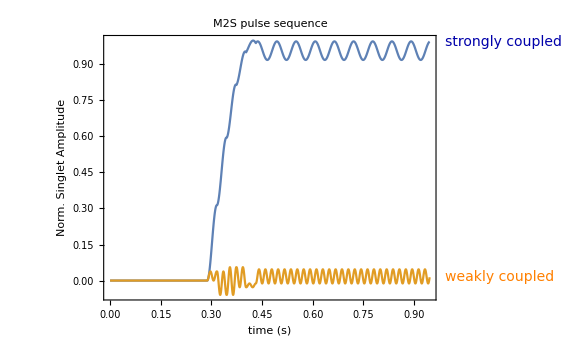

```mathematica
Plot[{trajSS1strong[t],trajSS1weak[t]},{t,0,Duration[M2SevS2M[Ω1,Ω2,J,1/(4J),n1[Ω1,Ω2,J],n1[Ω1,Ω2,J]/2]]},PlotRange->All,FrameLabel->{"time (s)","Norm. Singlet Amplitude"},PlotLabel->"M2S pulse sequence",PlotLabels->{Style["strongly coupled",Darker[Blue]],Style["weakly coupled",Orange]},ImageSize->Large]
```

## SLIC comparison

```mathematica
Ω1=-2π*1.4;Ω2=2π*1.4;J=17.4;
```

```mathematica
trajSS2strong=Trajectory[opI["z"]->{-SS},SLIC[Ω1,Ω2,J,0.5]];
```

```mathematica
Ω1=-2π*25;Ω2=2π*25;J=17.4;
```

```mathematica
trajSS2weak=Trajectory[opI["z"]->{-SS},SLIC[Ω1,Ω2,J,0.5]];
```

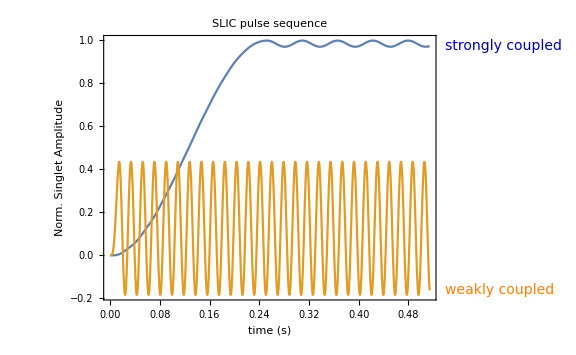

```mathematica
Plot[{trajSS2strong[t],trajSS2weak[t]},{t,0,Duration[SLIC[Ω1,Ω2,J,0.5]]},PlotRange->All,FrameLabel->{"time (s)","Norm. Singlet Amplitude"},PlotLabel->"SLIC pulse sequence",PlotLabels->{Style["strongly coupled",Darker[Blue]],Style["weakly coupled",Orange]},ImageSize->Large]
```

## SS-EXSY comparison

```mathematica
Ω1=-2π*1.4;Ω2=2π*1.4;J=17.4;
```

```mathematica
trajSS3strong=Trajectory[opI["z"]->{-SS},SarkarSeqII[Ω1,Ω2,J,0.5]];
```

```mathematica
Ω1=-2π*25;Ω2=2π*25;J=17.4;
```

```mathematica
trajSS3weak=Trajectory[opI["z"]->{-SS},SarkarSeqII[Ω1,Ω2,J,0.5]];
```

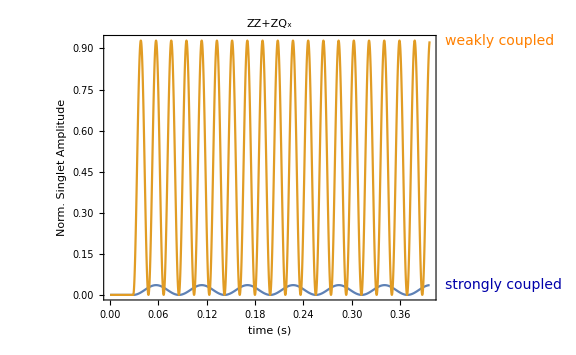

```mathematica
Plot[{trajSS3strong[t],trajSS3weak[t]},{t,0,Duration[SarkarSeqII[Ω1,Ω2,J,0.358]]},PlotRange->All,FrameLabel->{"time (s)","Norm. Singlet Amplitude"},PlotLabel->"ZZ+ZQ_x",PlotLabels->{Style["strongly coupled",Darker[Blue]],Style["weakly coupled",Orange]},ImageSize->Large]
```

# Analytical expressions for coherent evolution

```mathematica
matFP=MatrixExp[-ⅈ*MatrixRepresentation[Ω1*opI[1,"z"]+Ω2*opI[2,"z"]+2π*J*opI[1,"z"].opI[2,"z"]]*t];
matFPi=MatrixExp[ⅈ*MatrixRepresentation[Ω1*opI[1,"z"]+Ω2*opI[2,"z"]+2π*J*opI[1,"z"].opI[2,"z"]]*t];
matpulse=MatrixExp[-ⅈ*MatrixRepresentation[2π*ω*opI["x"]+2π*J*opI[1].opI[2]]*t ];
matpulsei=MatrixExp[ⅈ*MatrixRepresentation[2π*ω*opI["x"]+2π*J*opI[1].opI[2]]*t ];
```

## Free preession evolution of ZQx and LLC

```mathematica
ZQx=opI[1,"x"].opI[2,"x"]+opI[1,"y"].opI[2,"y"];
LLC=opI[1,"x"]-opI[2,"x"];
```

```mathematica
ExpToTrig[ExpressOperator[Operator[matFP.MatrixRepresentation[ZQx].matFPi],CartesianProductOperatorBasis[]]]//Simplify
```

Cos[t (Ω1-Ω2)] (I_(1x)•I_(2x))+Cos[t (Ω1-Ω2)] (I_(1y)•I_(2y))+(-(I_(1x)•I_(2y))+I_(1y)•I_(2x)) Sin[t (Ω1-Ω2)]

```mathematica
ExpToTrig[ExpressOperator[Operator[matFP.MatrixRepresentation[LLC].matFPi],CartesianProductOperatorBasis[]]]//Simplify
```

Cos[J π t] Cos[t Ω1] I_(1x)-Cos[J π t] Cos[t Ω2] I_(2x)+2 Cos[t Ω1] (I_(1y)•I_(2z)) Sin[J π t]-2 Cos[t Ω2] (I_(1z)•I_(2y)) Sin[J π t]+Cos[J π t] I_(1y) Sin[t Ω1]-2 (I_(1x)•I_(2z)) Sin[J π t] Sin[t Ω1]-Cos[J π t] I_(2y) Sin[t Ω2]+2 (I_(1z)•I_(2x)) Sin[J π t] Sin[t Ω2]

## CW evolution of ZQx and LLC

```mathematica
ZQx=opI[1,"x"].opI[2,"x"]+opI[1,"y"].opI[2,"y"];
LLC=opI[1,"x"]-opI[2,"x"];
```

```mathematica
ExpToTrig[ExpressOperator[Operator[matpulse.MatrixRepresentation[ZQx].matpulsei],CartesianProductOperatorBasis[]]]//FullSimplify
```

1/2 (2 (I_(1x)•I_(2x))+(1+Cos[4 π t ω]) (I_(1y)•I_(2y))+2 (I_(1z)•I_(2z)) Sin[2 π t ω]^2+(I_(1y)•I_(2z)+I_(1z)•I_(2y)) Sin[4 π t ω])

```mathematica
ExpToTrig[ExpressOperator[Operator[matpulse.MatrixRepresentation[LLC].matpulsei],CartesianProductOperatorBasis[]]]//Simplify
```

Cos[2 J π t] I_(1x)-Cos[2 J π t] I_(2x)+2 (I_(1y)•I_(2z)-I_(1z)•I_(2y)) Sin[2 J π t]